```mathematica
SetDirectory["D:\\Users\\Matt\\OneDrive\\Documents\\Course Notes\\Calculus 2\\Figures"]; (* for home desktop *)
```

```mathematica
rotationmark[x_, y_, r_, xscale_:1, yscale_:1]:=Graphics[{Thick, Red, Arrowheads[{0.0375}],
Arrow@BSplineCurve[Table[{r*xscale*Cos[t]+x, r*yscale*Sin[t]+y}, {t, 0, 11Pi/6, Pi/120}]]
}]
```

```mathematica
SetDirectory["C:\\Users\\matth\\OneDrive\\Mathematics\\calculus-notes\\Figures"];(* For laptop *)
```

```mathematica
vp=Options[Graphics3D,ViewPoint][[1,2]];
```

## Applications of Integrals

## Areas Between Curves

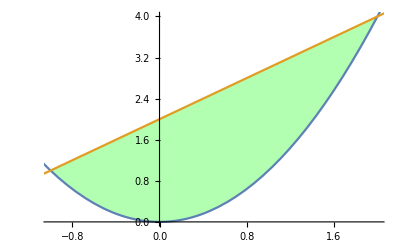

```mathematica
arealineparabola = Show[
Plot[{x^2, x+2}, {x, -1, 2},  TicksStyle->10,PlotStyle->Opacity[0],Filling->{1->{2}}, FillingStyle->Directive[Green, Opacity[0.3]]],
Plot[{x^2, x+2}, {x, -1.5, 2.5}]
]
Export["arealineparabola.pdf", arealineparabola];
```

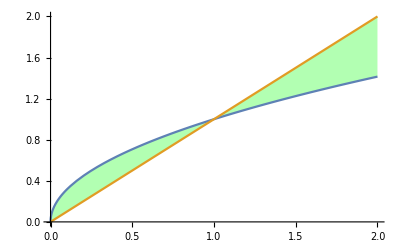

```mathematica
areasqrt = Show[
Plot[{Sqrt[x], x}, {x, 0, 2}, TicksStyle->10, Filling->{1->{2}}, FillingStyle->Directive[Green, Opacity[0.3]]]
]
Export["areasqrt.pdf", areasqrt];
```

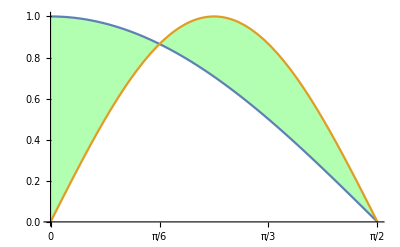

```mathematica
areatrig2xident = Show[
Plot[{Cos[x], Sin[2x]}, {x, 0, Pi/2}, Ticks->{Table[k*Pi/6 ,{k, 0, 3}], Automatic},TicksStyle->10,Filling->{1->{2}}, FillingStyle->Directive[Green, Opacity[0.3]]]
]
Export["areatrig2xident.pdf", areatrig2xident];
```

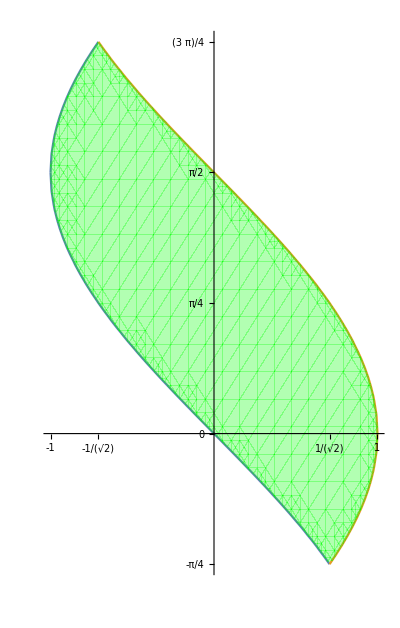

```mathematica
areawrty =Show[
ContourPlot[{x==-Sin[y], x==Cos[y]}, {x, -1, 1},{y, -Pi/4, 3Pi/4}, AspectRatio->Pi/2, Frame->False, AxesOrigin->{0,0}, Axes->True, TicksStyle->14,Ticks->{{-1, -√2/2, √2/2,1}, Table[k*Pi/4, {k, -1, 4,1}]}],
RegionPlot[-Sin[y]<x<Cos[y], {x, -1, 1},{y, -Pi/4, 3Pi/4}, BoundaryStyle->None, PlotStyle->Directive[Green, Opacity[0.3]]]
]
Export["areawrty.pdf", areawrty];
```

## Volumes by Cross Sections

```mathematica
volcsparabola = Show[
Plot[x^2, {x, 0, 1}, PlotRange->{Automatic, {-0.2, 1}},Filling->Axis, FillingStyle->Directive[Green, Opacity[0.3]]],
Plot[0, {x, 0, 1}, PlotRange->{Automatic, {-0.2, 1}}, PlotStyle->Directive[Thick, Red, Dashed]],
rotationmark[0.8, 0, 0.05, 0.4, 1.4]
]
Export["volcsparabola.pdf", volcsparabola];
```

-Graphics-

```mathematica
SetDirectory["C:\\Users\\matth\\OneDrive\\Mathematics\\calculus-notes\\Figures"]
```

C:\Users\matth\OneDrive\Mathematics\calculus-notes\Figures

```mathematica
volDiscSQrt=Show[
Plot[4-√x, {x, 0, 16}, PlotRange->{Automatic, {0, 5}},Filling->4, FillingStyle->Directive[Green, Opacity[0.3]]],
Plot[4, {x, 0, 16}, PlotRange->{Automatic, {0, 5}}, PlotStyle->Directive[Thick, Red, Dashed]],
rotationmark[12, 4, 0.4, 0.8, 1.4]
]
Export["vol-Disc-SQrt.pdf", volDiscSQrt];
```

-Graphics-

```mathematica
volcstrigshift=Show[
Plot[1+ Cos[x], {x, 0, Pi/2}, PlotRange->{Automatic, {0, 2}},Filling->1, FillingStyle->Directive[Green, Opacity[0.3]]],
Plot[1, {x, 0, Pi/2}, PlotRange->{Automatic, {0, 2}}, PlotStyle->Directive[Thick, Red, Dashed]],
rotationmark[0.8, 1, 0.1, 0.4, 1.4]
]
Export["volcstrigshift.pdf", volcstrigshift];
```

-Graphics-

```mathematica
volscsqrtwrty=Show[
Plot[Sqrt[x], {x, 0, 1}, PlotRange->{{-1.2, 1}, {0, 1}},Filling->Top, FillingStyle->Directive[Green, Opacity[0.3]]],
ContourPlot[x==-1, {x, -2, 2}, {y, 0, 1}, ContourStyle->Directive[Red, Thick, Dashed]],
rotationmark[-1, 0.8, 0.1, 1.4, 0.4]
]
Export["volscsqrtwrty.pdf", volscsqrtwrty];
```

-Graphics-

```mathematica
Expand[(1+y^2)^2 - 1]
```

2 y^2+y^4

```mathematica
Integrate[%, {y, 0, 1}]
```

13/15

## Volumes by Cylindrical Shells

```mathematica
volshparabola=Show[
Plot[4-(x-2)^2, {x, 0, 4}, PlotRange->{{-.2, 4}, {0, 4}},Filling->Axis, FillingStyle->Directive[Green, Opacity[0.3]]],
ContourPlot[x==0, {x, -2, 2}, {y, 0, 4}, ContourStyle->Directive[Red, Thick, Dashed]],
rotationmark[0,3, 0.1, 1.4, 1]
]
Export["volshparabola.pdf", volshparabola];
```

-Graphics-

```mathematica
Expand[x*(4-(x-2)^2)]
```

4 x^2-x^3

```mathematica
Integrate[%, {x, 0, 4}]
```

64/3

```mathematica
volshrecip=Show[
Plot[1/x, {x, 1, 2}, PlotRange->{{-2.2, 2}, {0, 4}},PlotStyle->Opacity[0],Filling->Axis, FillingStyle->Directive[Green, Opacity[0.3]]],
Plot[1/x, {x, 0, 4}, PlotRange->{{-2.2, 2}, {0, 4}}],
ContourPlot[x==-2, {x, -2.1, 2}, {y, 0, 4}, ContourStyle->Directive[Red, Thick, Dashed]],
rotationmark[-2,3, 0.1, 1.4, 1]
]
Export["volshrecip.pdf", volshrecip];
```

-Graphics-

```mathematica
volshexp=Show[
Plot[Exp[-x^2], {x, 0, 1}, PlotRange->{{-0.2, 1}, {0, 1.5}},Filling->Axis, FillingStyle->Directive[Green, Opacity[0.3]]],
ContourPlot[x==0, {x, -0.2,2}, {y, 0, 4}, ContourStyle->Directive[Red, Thick, Dashed]],
rotationmark[0,1.2, 0.08, 1.4, 1]
]
Export["volshexp.pdf", volshexp];
```

-Graphics-

```mathematica
volshwrty=Show[
Plot[Sqrt[x/3], {x, 0, 3}, PlotRange->{{-0.2, 3}, {-2.4, 1.5}},Filling->1, FillingStyle->Directive[Green, Opacity[0.3]]],
Plot[-2, {x, 0, 3}, PlotStyle->Directive[Red, Thick, Dashed]],
rotationmark[1.5,-2, 0.1, 0.5, 2]
]
Export["volshwrty.pdf", volshwrty];
```

-Graphics-

```mathematica
volshtwofunc = Show[
Plot[{x, √(2x)}, {x, 0, 2}, PlotRange->{{-1.2, 2}, {0, 2.2}},Filling->{1->{2}}, FillingStyle->Directive[Green, Opacity[0.3]]],
ContourPlot[x==-1, {x, -2, 3}, {y, -3, 3},ContourStyle->Directive[Red, Thick, Dashed]],
rotationmark[-1,2, 0.1, 2, 1]
]
```

-Graphics-

```mathematica
Export["volshtwofunc.pdf", volshtwofunc]
```

volshtwofunc.pdf

```mathematica
Integrate[(x+1)(√(2x)-x), x]//TraditionalForm
```

2/5 √2 x^(5/2)+2/3 √2 x^(3/2)-x^3/3-x^2/2

## Arc Length

```mathematica
pts = {{0,0}, {0.25,0.75},{1,1}};
delta = 0.3;
```

```mathematica
arclengthfunc = Show[
Graphics[{Blue, Thick, BSplineCurve[pts], Red, Line[{pts[[1]], pts[[3]]}], Darker@Green, Line[{{0.375 - delta, 0.625-delta},{0.375 + delta, 0.625 + delta}}],  Dashed,Line[{{0.375, 0.625},{0.375, 0}}],Red, Line[{{0,0},{1,0},{1,1}}], Text[Style[TraditionalForm["Cell["Δx",ExpressionUUID->"7c2525b8-c000-4aba-a5ca-7c8c037382cb"]"], 14], {0.5, 0.05}],Text[Style[TraditionalForm["Cell["Δy",ExpressionUUID->"0a9848da-e917-4c71-905f-d816b783388d"]"], 14], {0.95, 0.5}], Darker@Green, Text[Style[TraditionalForm["Cell["x",ExpressionUUID->"1bd72894-600c-4876-9935-b3f28724645f"]"], 14], {0.375, -0.04}]}]
, Axes->True, Ticks->None]
```

-Graphics-

```mathematica
Export["arclengthfunc.pdf", arclengthfunc]
```

arclengthfunc.pdf

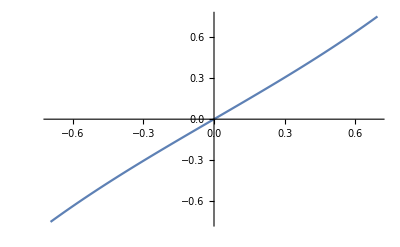

```mathematica
arclengthexp =Plot[(Exp[x]-Exp[-x])/2, {x, -Log[2], Log[2]}]
```

```mathematica
Export["arclengthexp.pdf", arclengthexp]
```

arclengthexp.pdf

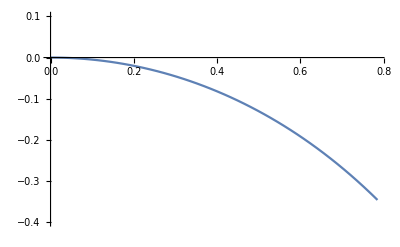

```mathematica
arclengthlncos = Plot[Log[Cos[x]], {x, 0, Pi/4}, PlotRange->{Automatic, {-0.4, 0.1}}]
```

```mathematica
Export["arclengthlncos.pdf", arclengthlncos];
```

```mathematica
Integrate[Sec[x], {x, 0, Pi/4}]
```

```mathematica
2 ArcTanh[Tan[π/8]]//TrigToExp
```

```mathematica
ArcCoth[x]//TrigToExp
```

-1/2 Log[1-1/x]+1/2 Log[1+1/x]

```mathematica
FullSimplify[%, x==√2]
```

```mathematica
1/2 Log[3+2 √2]
```

```mathematica
FullSimplify[√(3+2 √2)]
```

1+√2

## Surface Area of Revolution

```mathematica
surfarearev =Show[
RevolutionPlot3D[4-1/2*x, {x, 0.5, 1.5}, RevolutionAxis->{1, 0, 0}, Mesh->None, PlotRange->{{0,2},{-4, 4},{-4,4}}, Boxed->False, Axes->{True, False, True}, AxesOrigin->{0,0,0}, BoxRatios->{1, 1, 1}, ViewPoint->Front, Ticks->None,ImageSize->Large, PlotStyle->Opacity[0.4]],
Graphics3D[{
Arrowheads[0.02],
Arrow[{{0.5,0,0},{0.5, 0, 3.75}}],
Arrow[{{1.5,0,0},{1.5, 0, 3.25}}],
Arrow[{{1,0,0},{1, 0, 3.5}}],
Arrowheads[{-0.005, 0.005}],
Arrow[{{0.5,0,4},{1.5, 0, 3.5}}],
Text[Style[ToExpression["r_{1}", TeXForm, HoldForm],36], {1.6, 0, 1.52}],
Text[Style[ToExpression["r_{2}", TeXForm, HoldForm],36], {0.6, 0, 1.52}],
Text[Style[ToExpression["r", TeXForm, HoldForm],36], {1.1, 0, 1.52}],
Text[Style[ToExpression["\\Delta L", TeXForm, HoldForm],36], {1, 0, 4.2}]
}]
, Method->{"ShrinkWrap"->True}]
Export["surfarearev.png", surfarearev, ImageResolution->300]
```

-Graphics3D-

surfarearev.png

## Physical Applications

```mathematica
vp=Options[Graphics3D,ViewPoint][[1,2]];
prismtank = Graphics3D[
{
Opacity[0.1],
Prism[{{0,0,0},{-1, 0, 1}, {1, 0, 1},{0,-3,0},{-1, -3, 1}, {1, -3, 1}}],
Opacity[1],
Arrowheads[{-0.02, 0.02}],
Arrow[{{0, 0, -0.2}, {0, -3, -0.2}}],
Arrow[{{1.2, 0, 0}, {1.2, 0, 1}}],
Arrow[{{1, 0, 1.2}, {-1, 0, 1.2}}],
Text[Style["2 m",  18, FontFamily->"Times New Roman"], {0,0,1.4}],
Text[Style["1 m",  18, FontFamily->"Times New Roman"], {1.4,0,0.5}],
Text[Style["3 m",  18, FontFamily->"Times New Roman"], {0,-1.5,-0.4}],
Opacity[0.7], RGBColor[0.5,0.5,1.],
Cuboid[{-.699,0,.7},{.699,-2.99, .75}]
},
Boxed->False,ViewPoint->Dynamic[vp], ImageSize->Large, Lighting->"Neutral", Method->{"ShrinkWrap"->True}
]
```

-Graphics3D-

```mathematica
Dynamic[vp]
```

```mathematica
Export["prismtank.png", prismtank, ImageResolution->300]
```

prismtank.png

```mathematica
workbowl = Show[
SphericalPlot3D[1, {p, Pi/2, Pi}, {t, 0, 2Pi}, Mesh->None, PlotStyle->Directive[Opacity[0.5],Specularity[Gray,100], RGBColor[.8,.8,.8]], Boxed->False, Axes->False, PlotPoints->100,Lighting->"Neutral"],
Graphics3D[{
Arrowheads[0.02],
Arrow[{{0,0,0}, {1,0,0}}],
Text[Style["0.2 m", 18, FontFamily->"Times New Roman"], {0.5, 0, 0.1}],
Opacity[0.5], RGBColor[0.5,0.5,1.], Cylinder[{{0,0,-0.3}, {0,0,-0.35}}, .954]
}],ViewPoint->, ImageSize->Large,Method->{"CylinderPoints"->{400,1}, "ShrinkWrap"->True}
]
```

```mathematica
Export["workbowl.png", workbowl, ImageResolution->300]
```

workbowl.png

## Improper Integrals

```mathematica
Plot[{1/x + .08Sin[8x]/x,1/x + .08Sin[6x]/x + 1 }, {x, 0, 2}, Filling->Axis,PlotRange->{Automatic, {0,6}}, PlotLegends->Automatic, PlotStyle->{Dashed, Automatic}]
```

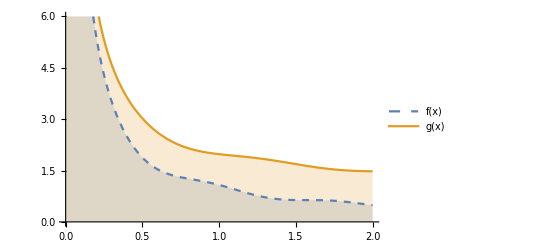
```mathematica
improperComp=-Graphics-;
```

```mathematica
Export["improperComp.pdf", improperComp];
```

## Series

```mathematica
Snowflake[i_]:=With[{c = KochCurve[i]}, Show[
Graphics[c, PlotRange->{{0,1.05}, {-0.9,0.3}}, ImageSize->Large],
Graphics[Translate[Rotate[c, 2Pi/3, {1/2,0}], {-1/4, -√3/4}]],
Graphics[Translate[Rotate[c, -2Pi/3, {1/2,0}], {1/4, -√3/4}]]
]];
```

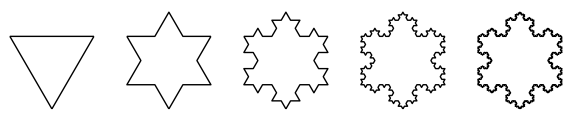

```mathematica
snowflakes = GraphicsRow[Table[Snowflake[i], {i, 0, 4}], ImageSize->Large]
```

```mathematica
Export["snowflaskes.pdf", snowflakes];
```

## Integral Test

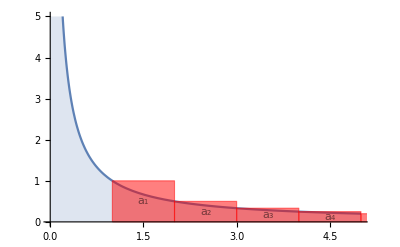

```mathematica
f[x_]:=1/x;
inttestdiv = Show[
Plot[f[x], {x, 0, 5}, PlotRange->{Automatic, {0,5}}, Filling->Axis],
Graphics[{Red, Opacity[0.5], EdgeForm[Red], Table[{Rectangle[{i,0},{i+1, f[i]}], Text[Style[Subscript["a",ToString[i]], Black], {(2i+1)/2, f[i]/2}]}, {i, 1, 5}]
}]
]
```

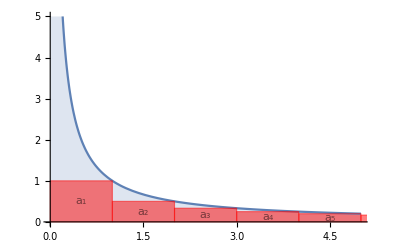

```mathematica
inttestconv = Show[
Plot[f[x], {x, 0, 5}, PlotRange->{Automatic, {0,5}}, Filling->Axis],
Graphics[{Red, Opacity[0.5], EdgeForm[Red], Table[{Rectangle[{i,0},{i+1, f[i+1]}], Text[Style[Subscript["a",ToString[i+1]], Black], {(2i+1)/2, f[i+1]/2}]}, {i, 0, 5}]}]
]
```

```mathematica
Export["inttestconv.pdf", inttestconv];
Export["inttestdiv.pdf", inttestdiv];
```

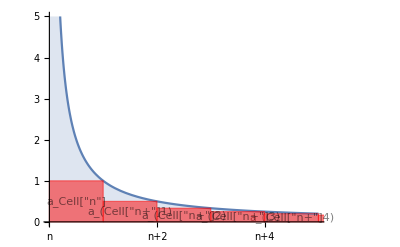

```mathematica
inttestremainderub = Show[
Plot[f[x], {x, 0, 5}, 
PlotRange->{Automatic, {0,5}}, 
Filling->Axis,
Ticks->{{{0,"n"}}∪Table[{i, Text[Style["n+"<>ToString[i], Black]]}, {i, 1, 5}], Automatic}
],
Graphics[{Red, Opacity[0.5], EdgeForm[Red],
Rectangle[{0,0},{1,1}],
Text[Style[Subscript["a","Cell["n",ExpressionUUID->"24d8964f-f407-4a88-9691-fe1cca4f3ac0"]"], Black], {1/2, 1/2}],Table[{Rectangle[{i,0},{i+1, f[i+1]}], Text[Style[Subscript["a","Cell["n+",ExpressionUUID->"53a1b93d-bbd6-4668-b763-68679fc0627a"]"<>ToString[i]], Black], {(2i+1)/2, f[i+1]/2}]}, {i, 1, 5}]}]
]
```

## Alternating Series

```mathematica
a[n_]:=4*(-1)^(n-1)/(2n-1);
s[n_]:=Sum[a[k], {k, 1, n}];
```

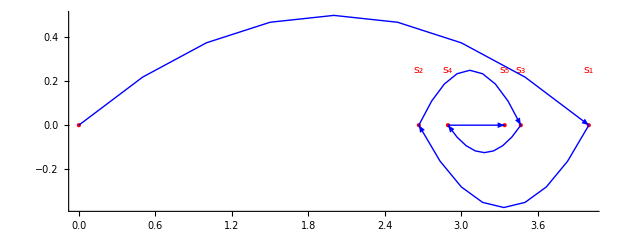

```mathematica
labels = {"","s_1", "s_2", "s_3", "s_4", "s_5"};
i = 1;
altseriestest  =Show[
NumberLinePlot[List/@Prepend[Table[s[n], {n, 1, 5}], 0], Spacings->0, PlotStyle->Directive[PointSize[Large],Red]]/.Point[x_]:>{Point[x],Text[labels[[i++]],{0,1/4}+x]},
Graphics[{Blue, Arrowheads[0.015],Arrow[BezierCurve[{{0,0}, {s[1]/2, 1},{s[1],0}}]],Table[Arrow[BezierCurve[{{s[n],0},{(s[n]+s[n+1])/2, (-1)^n(1-0.25*n)}, {s[n+1],0}}]], {n, 1, 4}]}], Method->{"ShrinkWrap"->True}
]
```

```mathematica
Export["altseriestest.pdf", altseriestest];
```

### Sum of Natural Numbers

```mathematica
Plot[x(x+1)/2, {x, -1.2, .2}, Filling->Axis, FillingStyle->{Directive[Red, Opacity[0.5]], Directive[Green, Opacity[0.5]]}]
```

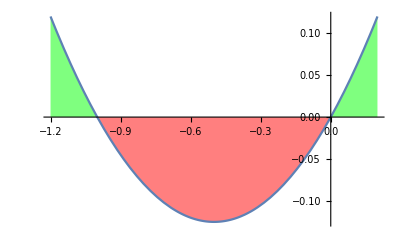

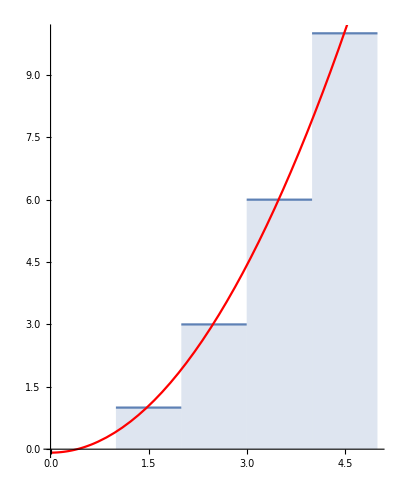

```mathematica
Show[
DiscretePlot[n(n+1)/2, {n, 1, 4}, ExtentSize->Right, PlotRange->{{0, 5}, Automatic}, AspectRatio->5/4],
Plot[-1/12+.5 x^2, {x, 0, 6}, PlotStyle->Red]
]
```

## Curves in the Plane

## Parametric Equations

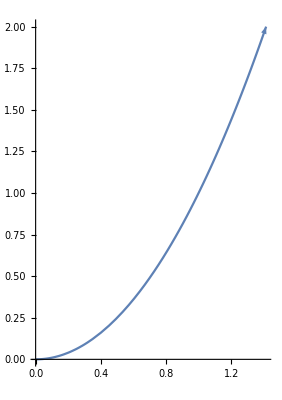

```mathematica
parapara = ParametricPlot[{Sqrt[t], t}, {t, 0, 2}, TicksStyle->12]/.Line[x_]:>{Arrowheads[{{0,0}, {0.04, 0.25}, {0.04, 0.5}, {0.04, 0.75}, {0.04,1}}],Arrow[x]}
```

```mathematica
Export["parapara.pdf", parapara];
```

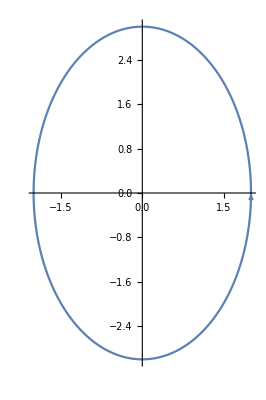

```mathematica
paraellipse = ParametricPlot[{2Cos[t], 3Sin[t]}, {t, 0, 2Pi}, TicksStyle->12]/.Line[x_]:>{Arrowheads[{{0,0}}∪Table[{0.04, 0.125*n}, {n, 1, 7}]],Arrow[x], PlotRange->{{0,1}, {0,1}}}
```

```mathematica
Export["paraellipse.pdf", paraellipse];
```

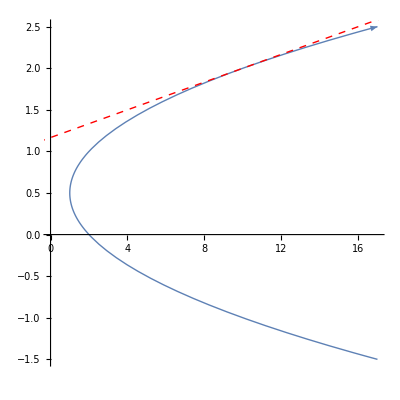

```mathematica
paraslope = Show[
ParametricPlot[{t^2 + 1, 1/2*(t+1)}, {t, -4,4}, AspectRatio->1, TicksStyle->18, PlotStyle->Thick]/.Line[x_]:>{Arrowheads[{{0,0}, {0.04, 0.25}, {0.04, 0.5}, {0.04, 0.75}, {0.04,1}}],Arrow[x], PlotRange->{{0,1}, {0,1}}},
Plot[1/12*x + 7/6, {x, -2, 20}, PlotStyle->Directive[Thick, Red, Dashed]]
]
```

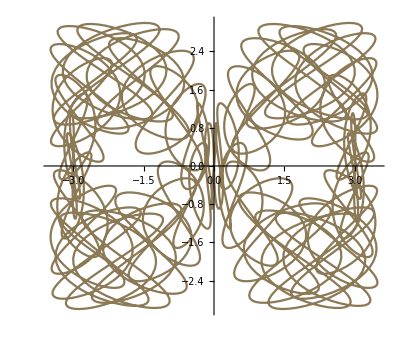

```mathematica
Export["paraslope.pdf", paraslope];
paraint1 = ParametricPlot[{3Cos[t] + Sin[2t]Cos[90t], 2Sin[2t]+Sin[60t]}, {t, 0, 2Pi}, ColorFunction->"DarkRainbow"]
```

```mathematica
Export["paraint1.pdf", paraint1];
```

## Polar Coordinates

```mathematica
Show[
PolarPlot[3, {t, 0, 2Pi}, PolarAxes-> Automatic, PolarGridLines->{Table[k*Pi/6, {k, 0, 12}], Range[1,5]}, GridLinesStyle-> Dotted,PlotStyle->Opacity[0], TicksStyle-> 8, PolarTicks->{Table[k*Pi/6, {k, 0, 11}], Automatic}, ImageSize->300,  PlotRange->6, PlotRangePadding->Scaled[.05]],
Graphics[{Blue, Circle[{0,0}, 1, {0, Pi/3}], Red, Thick, Line[{{0,0}, {√2,√6}}], PointSize[Large],Point[{√2,√6}]}]
]
```

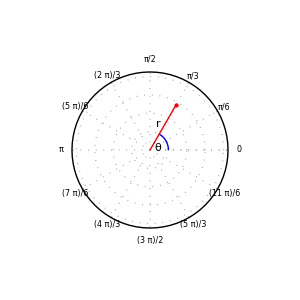
```mathematica
polarpoint=-Graphics-;
```

```mathematica
Export["polarpoint.pdf", polarpoint];
```

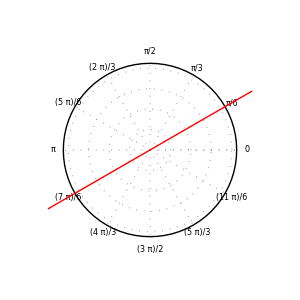

```mathematica
polarthetaline=Show[
PolarPlot[3, {t, 0, 2Pi}, PolarAxes-> Automatic, PolarGridLines->{Table[k*Pi/6, {k, 0, 12}], Range[1,5]}, GridLinesStyle-> Dotted,PlotStyle->Opacity[0], TicksStyle-> 8, PolarTicks->{Table[k*Pi/6, {k, 0, 11}], Automatic}, ImageSize->300,  PlotRange->6, PlotRangePadding->Scaled[.05]],
Plot[1/√3*x, {x, -5, 5}, PlotStyle->Directive[Red, Thick]]
]
```

```mathematica
Export["polarthetaline.pdf", polarthetaline];
```

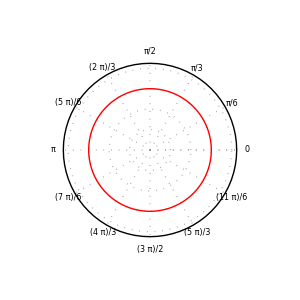

```mathematica
polarcircle=Show[
PolarPlot[3, {t, 0, 2Pi}, PolarAxes-> Automatic, PolarGridLines->{Table[k*Pi/6, {k, 0, 12}], Range[1,5]}, GridLinesStyle-> Dotted,PlotStyle->Directive[Red, Thick], TicksStyle-> 8, PolarTicks->{Table[k*Pi/6, {k, 0, 11}], Automatic}, ImageSize->300,  PlotRange->6, PlotRangePadding->Scaled[.05]]
]
```

```mathematica
Export["polarcircle.pdf", polarcircle];
```

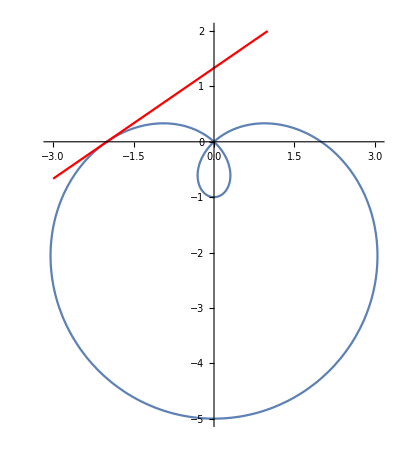

```mathematica
polarslope = Show[
PolarPlot[2-3Sin[t], {t, 0, 2Pi}, AspectRatio->7/6],
Plot[2/3*x +4/3, {x, -3, 3}, PlotStyle->Red, PlotRange->{Automatic, {-5,2}}]
]
```

```mathematica
Export["polarslope.pdf", polarslope];
```

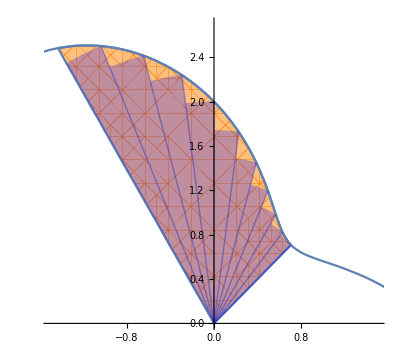

```mathematica
r[t_]:=2-Sin[2t]; 
polarrects=Show[
PolarPlot[r[t], {t, 0, 2Pi}, PlotRange->{{-1.5,1.5},{0,2.7}}],
RegionPlot[0≤(x^2+y^2)^(3/2)≤2(x^2+y^2)-2x*y && Pi/4≤ArcTan[x,y]≤2Pi/3, {x, -4, 4}, {y, -4, 4}, PlotStyle->Directive[Orange, Opacity[0.5]]],
Graphics[{Opacity[0.25],Blue,EdgeForm[{Gray, Thin}],Table[{Disk[{0,0}, r[Pi*k/24], {Pi*k/24, Pi*(k+1)/24}], Thin, Line[{{0,0}, {r[Pi*k/24]*Cos[Pi*k/24], r[Pi*k/24]*Sin[Pi*k/24]}}]}, {k,6,15} ]}]
]
```

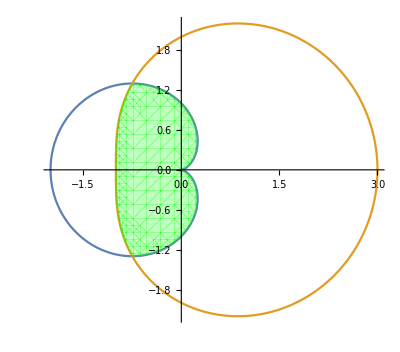

```mathematica
polarbetween = Show[
PolarPlot[{1-Cos[t], 2+Cos[t]}, {t, 0, 2Pi}],
RegionPlot[0≤ x^2 + y^2 ≤ (1-Cos[ArcTan[x,y]])^2 && 0 ≤ x^2 + y^2 ≤ (2+Cos[ArcTan[x,y]])^2, {x, -2, 2}, {y, -2, 2}, PlotStyle->Directive[Green, Opacity[0.25]], BoundaryStyle->None]
]
```

```mathematica
Export["polarbetween.png", polarbetween, ImageResolution->300];
```

## Conic Sections

```mathematica
conichyperbola = Show[
ParametricPlot3D[{v Cos[u],v Sin[u],v},{u,0,2Pi},{v,-1,1},Mesh->None,BoundaryStyle->None,PlotStyle->Directive[FaceForm[Blue,Yellow], Opacity[0.5]]],
ParametricPlot3D[{{-.5,1,0}+ u{0,-1,0} + v{0,0,1}}, {u, 0, 2}, {v, -1, 1}, Mesh->None, PlotStyle->Directive[Opacity[0.5], FaceForm[Red]]],
ContourPlot3D[{z^2-x^2-y^2, x + 0.5}, {x, -1, 1}, {y, -1, 1}, {z, -1, 1}, Contours->{0}, ContourStyle->Opacity[0], Mesh->None, BoundaryStyle->{1->None,2->None,{1,2}->{{Green, Thick}}}], ViewPoint->
]
```

-Graphics3D-

```mathematica
Export["conichyperbola.png", conichyperbola, ImageResolution->500];
```

```mathematica
conicparabola = Show[
ParametricPlot3D[{v Cos[u],v Sin[u],v},{u,0,2Pi},{v,-1,1},Mesh->None,BoundaryStyle->None,PlotStyle->Directive[FaceForm[Blue,Yellow], Opacity[0.5]]],
ParametricPlot3D[{{-.5,1,0}+ u{0,-1,0} + v{1,0,1}}, {u, 0, 2}, {v, -1, 1}, Mesh->None, PlotStyle->Directive[Opacity[0.5], FaceForm[Red]]],
ContourPlot3D[{z^2-x^2-y^2, z-x-0.5}, {x, -1, 1}, {y, -1, 1}, {z, -1, 1}, Contours->{0}, ContourStyle->Opacity[0], Mesh->None, BoundaryStyle->{1->None,2->None,{1,2}->{{Green, Thick}}}], ViewPoint->
]
```

-Graphics3D-

```mathematica
Export["conicparabola.png", conicparabola, ImageResolution->500];
```

```mathematica
coniccircle = Show[
ParametricPlot3D[{v Cos[u],v Sin[u],v},{u,0,2Pi},{v,-1,1},Mesh->None,BoundaryStyle->None,PlotStyle->Directive[FaceForm[Blue,Yellow], Opacity[0.5]]],
ParametricPlot3D[{{0,0,0.5}+ u{1,0,0} + v{0,1,0}}, {u, -1,1}, {v, -1, 1}, Mesh->None, PlotStyle->Directive[Opacity[0.5], FaceForm[Red]]],
ContourPlot3D[{z^2-x^2-y^2, z-1/2}, {x, -1, 1}, {y, -1, 1}, {z, -1, 1}, Contours->{0}, ContourStyle->Opacity[0], Mesh->None, BoundaryStyle->{1->None,2->None,{1,2}->{{Green, Thick}}}], ViewPoint->
]
```

-Graphics3D-

```mathematica
Export["coniccircle.png", coniccircle, ImageResolution->500];
```

```mathematica
{0,1,0.25} ×{1,0,0}
```

{0.,0.25,-1}

```mathematica
conicellipse = Show[
ParametricPlot3D[{v Cos[u],v Sin[u],v},{u,0,2Pi},{v,-1,1},Mesh->None,BoundaryStyle->None,PlotStyle->Directive[FaceForm[Blue,Yellow], Opacity[0.5]]],
ParametricPlot3D[{{0,0,0.5}+ u{0,1,0.25} + v{1,0,0}}, {u, -1,1}, {v, -1, 1}, Mesh->None, PlotStyle->Directive[Opacity[0.5], FaceForm[Red]]],
ContourPlot3D[{z^2-x^2-y^2, 1/4*y-z+1/2}, {x, -1, 1}, {y, -1, 1}, {z, -1, 1}, Contours->{0}, ContourStyle->Opacity[0], Mesh->None, BoundaryStyle->{1->None,2->None,{1,2}->{{Green, Thick}}}], ViewPoint->
]
```

-Graphics3D-

```mathematica
Export["conicellipse.png", conicellipse, ImageResolution->500];
```

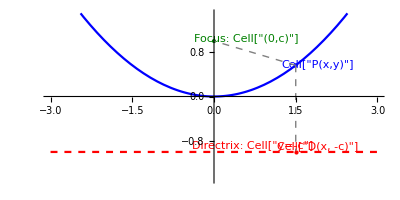

```mathematica
paraboladef =Show[
Plot[1/4*x^2, {x, -3, 3}, PlotStyle->Blue,PlotRange->{Automatic, {-1.5,1.5}}],
Plot[-1, {x, -3, 3}, PlotStyle->Directive[Dashed, Red]],
Graphics[{RGBColor[0,0.5,0], PointSize[Large], Point[{0,1}], Text[Style["Focus: Cell["(0,c)",ExpressionUUID->"2b5e1e8e-401c-4695-a643-40ef9bcaf408"]", RGBColor[0,.5,0]], {0.6,1.05}],Blue,Point[{1.5,0.5625}], Text["Cell["P(x,y)",ExpressionUUID->"1dc113c2-84e4-41aa-be04-25a0e68d6874"]", {1.9, .5625}],Text[Style["Directrix: Cell["y=-c",ExpressionUUID->"f6d8a620-d416-4598-9852-34656897c40a"]", Red], {0.7,-0.9}], Gray, Dashed, Line[{{1.5, 0.5625}, {1.5, -1}}], Line[{{1.5, 0.5625}, {0,1}}], Red, Point[{1.5, -1}], Text[Style["Cell["D(x, -c)",ExpressionUUID->"b7052ce0-e631-4265-be28-a2ec7cc668cd"]", Red], {1.9, -0.9}]}], AspectRatio->1/2
]
```

```mathematica
Export["paraboladef.pdf", paraboladef];
```

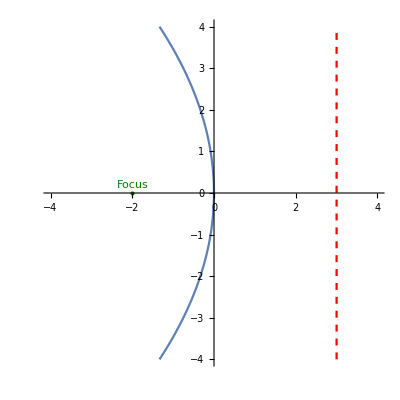

```mathematica
parabolaleft = Show[
ContourPlot[{y^2 == -12x, x==3},{x, -4, 4}, {y, -4, 4},ContourStyle->{Automatic, Directive[Dashed, Red]}, Frame->False, Axes->True],
Graphics[{RGBColor[0,.5,0], PointSize[Large], Point[{-2,0}], Text["Focus", {-2, 0.2}]}]
]
```

```mathematica
Export["parabolaleft.pdf", parabolaleft];
```

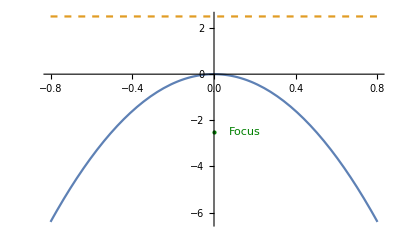

```mathematica
paraboladown = Show[
Plot[{-10x^2, 5/2}, {x, -0.8, 0.8}, PlotStyle->{Automatic, Dashed}],Graphics[{RGBColor[0,.5,0], PointSize[Large], Point[{0,-5/2}], Text["Focus", {0.15, -5/2}]}]
]
```

```mathematica
Export["paraboladown.pdf", paraboladown];
```

```mathematica
Directory[]
```

```mathematica
"D:\\Users\\Matt\\OneDrive\\Documents\\Course Notes\\Calculus 2\\Figures"
```

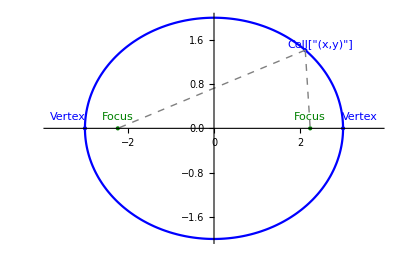

```mathematica
ellipsedef=Show[
ParametricPlot[{3Cos[t], 2Sin[t]}, {t, 0, 2Pi}, PlotStyle->Blue, PlotRange->{{-3.8,3.8}, Automatic}],
Graphics[{PointSize[Large], Blue, Point[{{-3,0}, {3,0},{3Cos[Pi/4], 2Sin[Pi/4]}}], Text["Cell["(x,y)",ExpressionUUID->"e2fa9c7d-ed58-47be-86f1-27c875108a0c"]", {3Cos[Pi/4]+0.36, 2Sin[Pi/4]+0.1}],Text["Vertex", {3.4, 0.2}],Text["Vertex", {-3.4, 0.2}],
RGBColor[0,0.5,0], Text["Focus", {-√5,0.2}],Text["Focus", {√5,0.2}],Point[{{-√5,0}, {√5,0}}], 
Gray, Dashed, Line[{{3Cos[Pi/4], 2Sin[Pi/4]}, {√5,0}}],Line[{{3Cos[Pi/4], 2Sin[Pi/4]}, {-√5,0}}]}]
, AspectRatio-> 2/3
]
```

```mathematica
Export["ellipsedef.pdf", ellipsedef]
```

ellipsedef.pdf

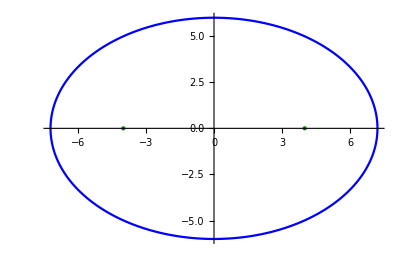

```mathematica
ellipseeqn=Show[
ParametricPlot[{√52 Cos[t], 6Sin[t]}, {t, 0, 2Pi}, PlotStyle->Blue],
Graphics[{PointSize[Large], Blue, RGBColor[0,0.5,0],Point[{{-4,0}, {4,0}}]}]
, AspectRatio-> 2/3
]
```

```mathematica
Export["ellipseeqn.pdf", ellipseeqn]
```

ellipseeqn.pdf

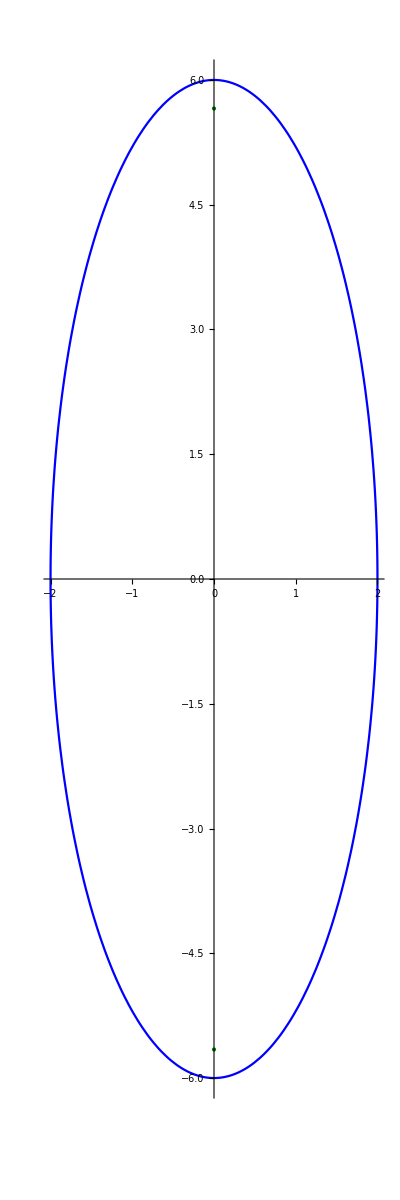

```mathematica
ellipseinfo= ellipseeqn=Show[
ParametricPlot[{2Cos[t], 6Sin[t]}, {t, 0, 2Pi}, PlotStyle->Blue],
Graphics[{PointSize[Large], Blue, RGBColor[0,0.5,0],Point[{{0, 4 √2}, {0,-4 √2}}]}]
, AspectRatio-> 3
]
```

```mathematica
Export["ellipseinfo.pdf", ellipseinfo];
```

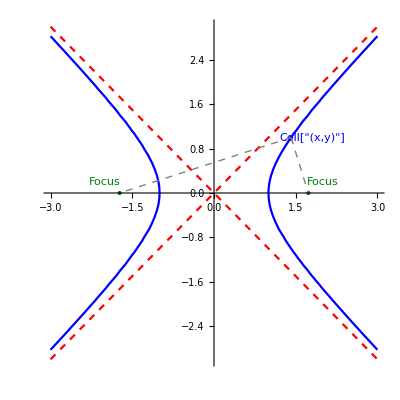

```mathematica
hyperboladef=Show[
ContourPlot[x^2-y^2==1, {x, -3,3}, {y, -3, 3}, Frame->False, Axes->True, ContourStyle->Blue],
Plot[{-x, x}, {x, -3, 3}, PlotStyle->Directive[Red, Dashed]],
Graphics[{Blue, PointSize[Large], 
Point[{√2,1}], Text["Cell["(x,y)",ExpressionUUID->"8185e546-dc06-42ff-ae3e-3972745e9e7d"]", {1.8, 1}],
RGBColor[0,0.5,0], Point[{-√3,0}], Point[{√3,0}],Text["Focus", {2, 0.2}],Text["Focus", {-2, 0.2}],
Gray, Dashed, Line[{{√2,1},{-√3,0}}], Line[{{√2,1},{√3,0}}]
}]
]
```

```mathematica
Export["hyperboladef.pdf", hyperboladef];
```

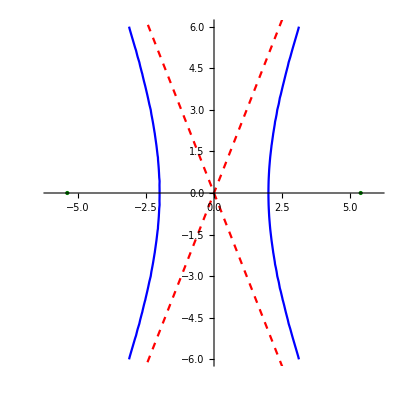

```mathematica
hyperbolaeqn = Show[
ContourPlot[25 x^2-4 y^2==100, {x, -6, 6}, {y, -6, 6}, Frame->False, Axes->True, ContourStyle->Blue],
Plot[{-5/2*x, 5/2*x}, {x, -6, 6}, PlotStyle->Directive[Red, Dashed]],
Graphics[{RGBColor[0,0.5,0], PointSize[Large], Point[{{-√29,0}, {√29,0}}]}]
]
```

```mathematica
Export["hyperbolaeqn.pdf", hyperbolaeqn];
```

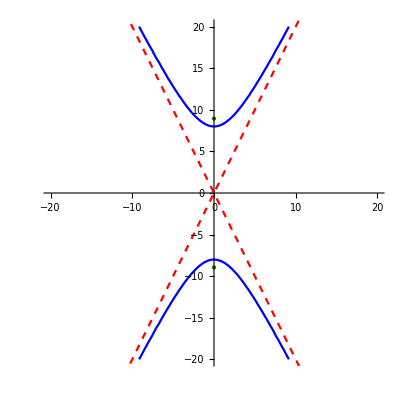

```mathematica
hyperbolaasymp = Show[
ContourPlot[y^2-4 x^2==64, {x, -20,20}, {y, -20,20}, Frame->False, Axes->True, ContourStyle->Blue],
Plot[{-2*x, 2*x}, {x, -15,15}, PlotStyle->Directive[Red, Dashed]],
Graphics[{RGBColor[0,0.5,0], PointSize[Large], Point[{{0, -4 √5}, {0,4 √5}}]}]
]
```

```mathematica
Export["hyperbolaasymp.pdf", hyperbolaasymp]
```

hyperbolaasymp.pdf

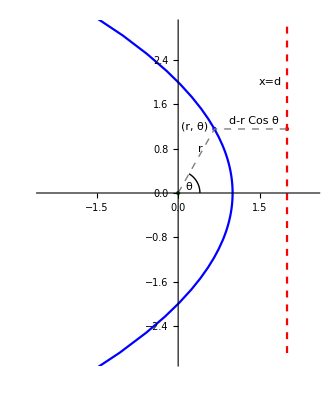

```mathematica
f[t_]:=2/(1+Cos[t]);
ppoint = {2/3,2/(√3)};
polarconic = Show[
PolarPlot[f[t], {t,-Pi + 0.1, Pi-0.1}, PlotRange->{{-2.5,2.5},{-3,3}}, PlotStyle->Blue ],
ContourPlot[x==2, {x, -3, 3}, {y, -3, 3},ContourStyle->Directive[Dashed, Red]],
Graphics[{
RGBColor[0,.5,0], PointSize[Large], Point[{0,0}],
Black, Style[Text["x=d", {1.7,2}], 12],Style[Text["θ", {0.2, 0.1}],12],Style[Text["r", {0.4, 0.8}],12],Style[Text["d-r Cos θ", {1.4, 1.3}],12],Style[Text["(r, θ)", {.3, 1.2}],12],Circle[{0,0}, 0.4, {0, Pi/3}],
Red,Point[{2,2/√3}],
Blue, Point[ppoint],
Gray, Dashed, Line[{{0,0}, ppoint, {2, 2/√3}}]
}]
]
```

```mathematica
Export["polarconic.pdf", polarconic];
```

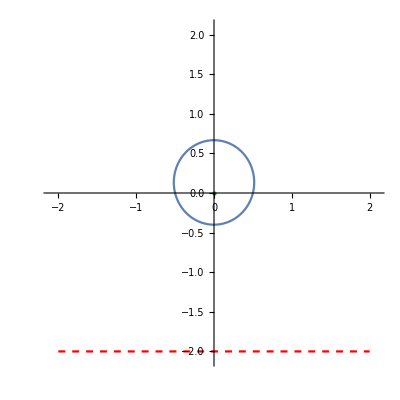

```mathematica
Show[
PolarPlot[2/(4-Sin[t]), {t, -Pi, Pi}, PlotRange->2.1],
Plot[-2, {x, -2, 2}, PlotStyle->Directive[Dashed, Red]],
Graphics[{
Darker[Green], PointSize[Large],Point[{0,0}]
}]
]
```

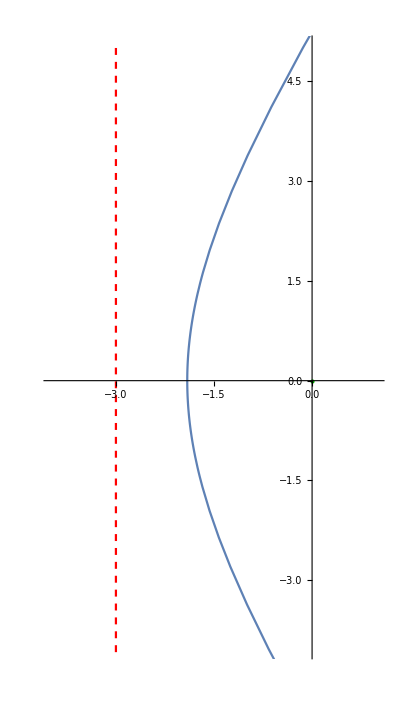

```mathematica
Show[
PolarPlot[21/(4-7Cos[t]), {t, -Pi, Pi}, PlotRange->{{-4, 1}, {-4,5}}, Exclusions-> {Cos[t]==4/7}, AspectRatio->9/5],
ContourPlot[x==-3, {x, -4,4 }, {y, -5,5}, ContourStyle->Directive[Dashed, Red]],
Graphics[{
Darker[Green], PointSize[Large],Point[{0,0}]
}]
]
```